ⅆx/ⅆt==10^-4 x^2-10^-2 x

y == x , x == t;

```mathematica
γ[x_,y_]:={1,10^-4 y^2-10^-2 y};
```

```mathematica
Integrate[1/(10^-4 y^2-10^-2 y),y]
```

10000 (1/100 Log[100-y]-Log[y]/100)

```mathematica
g[y_]:=10000 (1/100 Log[100-y]-Log[y]/100)
```

```mathematica
Solve[g[25]==0+C,C]
```

{{C→-100 (Log[25]-Log[75])}}

```mathematica
κ=-100 (Log[25]-Log[75]);
```

```mathematica
sols[x_]=NSolve[g[y]==x+κ,y];
```

```mathematica
numIndMeses=Table[sols[x],{x,0,2000}]; (* Período de 2000 meses - Jeito gambiarra de mostra a queda *)
```

```mathematica
numIndMeses[[2000]] (* Testando pelo table a diminuição do número de jacarés *)
```

{{y→6.93956×10^-8}}

### Campo de coeficientes angulares com a condição fornecida no instante inicial

#### Forma elegante que não sei interpretar pelo direction field

```mathematica
campo=VectorPlot[γ[x,y],{x,-3,4},{y,23,27},VectorStyle->{Arrowheads[0],Thin,Black},Background->RGBColor[0.7,0.86,0.85]];
```

```mathematica
ponto=Graphics[{PointSize[Large],Red,Point[{0,25}]}];
```

```mathematica
text=Graphics[{Text[Style["t = 0",Bold,Black],{0,25.2}]}];
```

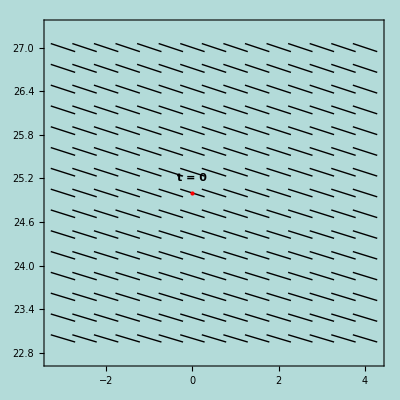

```mathematica
Show[campo,ponto,text]
```